```mathematica
importator[filename_]:=Module[{data},
data=Import[filename];
Select[Table[Rest/@Select[data,#[[1]]==i&],{i,0,4}],Length[#]>0&]
];
comparator[filename_]:=Module[{data,colours},
data=importator[filename];
colours={Red,Green,Blue,Black,Brown};
Show[Table[ListPlot[data[[i]],PlotRange->{0,1},Joined->True,PlotStyle->colours[[i]]],{i,1,Length[data]}]]
]
```

```mathematica
comparator["fabio.csv"]
```

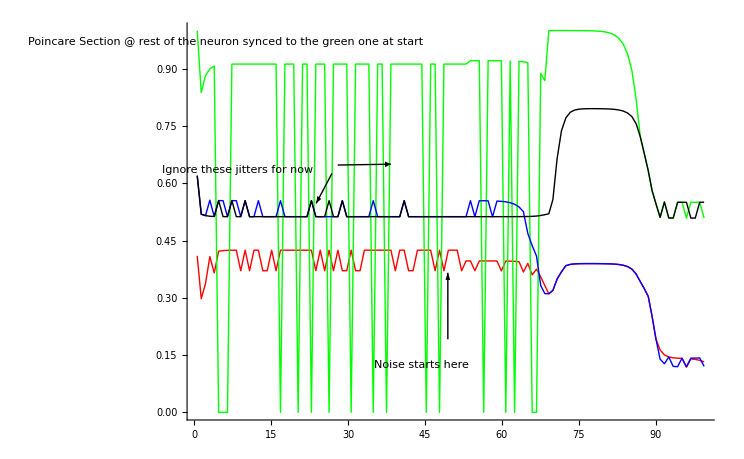

```mathematica
J=1.04;
y=1;
T=1/y * Log[J/(J-y)];
V=J/y *(1-Exp[-p T]);
V/.p->0.49
```

0.829285